```mathematica
densityList=Table[Import[NotebookDirectory[]<>"fixed/density"<>ToString[i]<>".json"],{i,1,168}];
```

```mathematica
meanPopulation=Mean[densityList];
```

```mathematica
locationList=Import[NotebookDirectory[]<>"useable/poi_data.json"]⟦All,7,2⟧;
```

```mathematica
serveyData=Import[NotebookDirectory[]<>"tel-servey/raw-result.json"];
```

```mathematica
ruledLocationList=Apply[Rule,Transpose[{locationList,Range[Length[locationList]]}],1];
nearestList=Nearest[ruledLocationList,#,20]&/@(#⟦1;;2⟧&/@serveyData);
```

```mathematica
uniformLocationList=locationList/.{{a_,b_}-> {a N[Sqrt[3]/2],b}};
uniformServeyLocation=serveyData⟦All,1;;2⟧/.{{a_,b_}->{a N[Sqrt[3]/2],b}};
nearestWeights=Map[1/(#.#)&,((uniformLocationList⟦#⟧&/@nearestList)-(Table[#,20]&/@uniformServeyLocation)),{2}];
```

```mathematica
populationAtServeyPoints=Mean/@Table[WeightedData[(meanPopulation⟦#⟧&/@nearestList)⟦i⟧,nearestWeights⟦i⟧],{i,1,Length[nearestWeights]}];
```

```mathematica
serveyScaleData=serveyData⟦All,3;;9⟧;
positive=N[#⟦1⟧+#⟦7⟧-2]&/@serveyScaleData;
negative=N[#⟦2⟧+#⟦6⟧-2]&/@serveyScaleData;
tiredness=N[(2#⟦3⟧+#⟦4⟧-2#⟦5⟧+8)/3]&/@serveyScaleData;
```

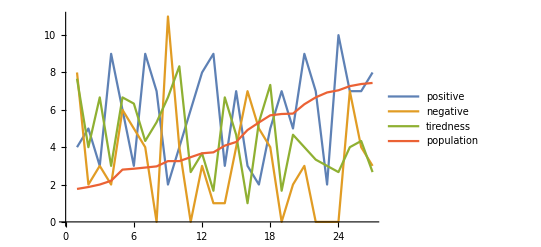

```mathematica
ListPlot[Transpose@SortBy[Transpose[{positive,negative,tiredness,Log@populationAtServeyPoints}],#⟦4⟧&], Joined->True,PlotLegends->{"positive","negative","tiredness","population"}]
```

```mathematica
{GeoHistogram[Apply[Rule,Transpose[{GeoPosition/@Reverse/@serveyData⟦All,1;;2⟧,positive}],1]],
GeoHistogram[Apply[Rule,Transpose[{GeoPosition/@Reverse/@serveyData⟦All,1;;2⟧,negative}],1]],
GeoHistogram[Apply[Rule,Transpose[{GeoPosition/@Reverse/@serveyData⟦All,1;;2⟧,tiredness}],1]]}
```

GeoGraphics::tiles: Unable to download 2 tiles of the geo background image.

General::stop: Further output of GeoGraphics::tiles will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
GeoHistogram[Apply[Rule,Transpose[{GeoPosition/@Reverse/@locationList,meanPopulation}],1],{"Total",150}]
```

-Graphics-